# 4T Modelling Thermodynamics and Equilibrium of mixture of radiation field, ionic gas and electron gas

## Constants and Functions

electron-ion collision cross sections
typically 10^(-11) m^2
https://www.nist.gov/system/files/documents/srd/jpcrd386.pdf

```mathematica
(* Initial parameters and constants *)

c= 3.0*10^(8)
ep0 = 8.8541878128*10^(−12);
kb = 1.380649*10^(−23);
ee = 1.602*10^(-19);
na=6.02*10^23; (* avogadros number*)

a = 2*10^(-10);
mp = 1.67262192*10^(-27);
md = 2.014102*mp;(*mass deuterium*)
mt= 3.016049*mp;(*mass tritium*)
mal = 4.002603*mp; (**)
hbar = 1.05457182 *10^(-34);
me = 9.1093837*10^(-31);
mme=me*na; (* molar electron mass*)
ui = 13.6 * ee;(* ionization energy for hydrogen*)

ar = 5.670374*10^(-8) ;(* stefan-boltzmann constant *)

sigmaie = 1.0*10^(-11); (* e- ion collision cross section  m^2*)
sigmaii  = Pi*a*a; (* ion ion collision cross section based on atomic size *)

(*Nuclear Constants for burning and transfer*)
sigt= (8/Pi)*(ee^2/(me*c*c))^2;  (*thompson cross section*)  
kevtok = 11604525.0061657; (* convert kev to kelvin*)
```

3.×10^8

3.×10^8

## Model Parameters

```mathematica
{{(*The model parameters*)
Ni=1; (* number of moles of ions in total*)
ni0 =Ni*na; (*initial number of moles of ions*)(*  amount of D and T *)
ne=2*ni0;  (* number of electrons*)

niini=1*na;te0=5; ti=5;
t0=0;
tf=0.0002;(*final time*)
h=(10)^(-10);(*step size*)}, {□}}
```

{{Null^7},{□}}

```mathematica
{{(* Saha equation*) (* Here calculate the ionization fraction *)
x[N_,T_, Ne_]:= ((2*Pi*me*kb/hbar)^(3/2))*(T^(3/2)/Ne)*Exp[-(ui/(kb*T))]; (* Ne is electron number density *) (* typical ne 10^(-20)*)

(* time between collisions ... relaxation time*)
taun[N_,T_]:=(1/(N*sigmaii))*Sqrt[mp/(kb*T)];
taue[Ne_,Te_]:=(1/(Ne*sigmaie))*Sqrt[me/(kb*Te)]}, {□}}
```

{{Null^3},{□}}

## Radiation and Perfect Gas

and Gas Perfect Radiation

```mathematica
pr[N_, Vo_, T_]:= (N*kb*T/Vo)+(ar*T^4)/3;
Et[N_,Vo_,T_]:= (3/2)*(N*kb*T)+(Vo*ar*T^4);
St[N_,Vo_,T_]:= N*kb*Log[Vo*T^(3/2)]+(4/3)*ar*Vo*T^3
```

## Radiation and Ionic Gas

```mathematica
(*   using saha equation  to get energy and pressure for ionic gas and radiation field*)
```

## Planck and Bose Einstein Distribution

```mathematica
(*  Planck distribution*)
```

```mathematica
npl[nu_,T_]:= 1.0/(Exp[2*Pi*hbar*nu/(kb*T)]-1.0)
```

```mathematica
(* Bose-Einstein distribution*)
```

```mathematica
nbe[nu_,mu_,T_]:= 1.0/(Exp[((2*Pi*hbar*nu)/(kb*T))-mu]-1.0)
```

```mathematica
fbe[ep_,al_]:= 1.0/(Exp[ep+al]-1.0);
```

## Rates for Nuclear Reactions

```mathematica
(* rates for nuclear reactions*)
```

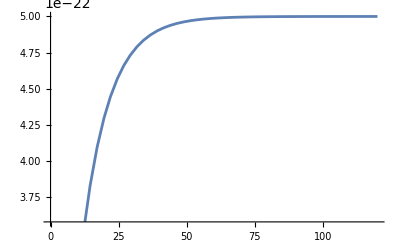

```mathematica
Adt=5.0*10^(-22); (* m^3/s*)
kdt=0.1;
T0dt=1;
sigvdt[T_]:=Adt*(T0dt-Exp[-kdt*T]);(*DT fusion reaction cross section sigv*) (*T is the temperature in keV*)
Plot[sigvdt[x1],{x1,0,120}]
```

```mathematica
"interactive plot"%62DynamicModule[{xc,dx},Manipulate[Plot[sigvdt[x1],{x1,xc-dx,xc+dx}],{{xc,60,"center"},-300,420},{{dx,60.,"zoom"},360,3.6}],DynamicModuleValues:>{}]
```

```mathematica
(* functions *)
nuc[ne_] := c*sigt*ne(* compton strength*);
lambda[te_,ne_]:= 25.127-Log[(ne^0.5)/(1000.0*te)];  (* keV *)
fali[te_]:= (te)/((te)+32);
eal:= ee*3.5*(10^6);(*MeV*)
al:=0.01;
em:=99999.0;


(*mme molar mass of electron*)
pei[ne_, ni_,te_,ti_]:=100000*(6/Sqrt[Pi])*nuc[ne]*ni*((mme/md)+(mme/mt)+4*((ni0-ni)/ni)*(mme/mal))*((me*c*c/(2*te))^(3/2))*Log[lambda[te,ne]]*(ti-te);
```

## Radiation Solver Section

```mathematica
(**)
k0[x]:=1.0;
Ib[alph_,gam_]:= ∫_0^em k0[x/2]*Exp[-x/2]*(Exp[alph+(x/gam)]-Exp[x])/(Exp[alph+(x/gam)]-1)ⅆx;(*complete this with integral definition*)
(**)
Ic[alph_,gam_]:= (1-gam)*∫_0^em (x^4)*Exp[alph+x]/(Exp[alph+x]-1)^2ⅆx;(*complete this with integral definition*)
(**)
f[alph_, tr_, te_ ]:=  (1.0/(4*(1-gam))*Ic[alph,tr/te] ;
```

```mathematica
(**)
prad[ni_,te_,ti_,tr_]:= tr^4;
```

```mathematica
(**)
```

```mathematica
(**)
```

## Rates of Change of ni, Te and Ti CHECK THE UNITS

```mathematica
f1[t_,ni_,te_,ti_]:=-(ni^2)*sigvdt[ti/kevtok];      (* dni/dt *)
f2[t_,ni_,te_,ti_]:=kevtok*(2/(3*ne))*((eal*(1-fali[te/kevtok]))*(ni^2)*sigvdt[ti/kevtok]   +pei[ne,ni,te,ti]  );(* dte/dt *) 
f3[t_,ni_,te_,ti_]:=kevtok*(2/(3*(ni+ni0)))*((eal*fali[te/kevtok]+(3*ti/2))*(sigvdt[ti/kevtok]*ni^2)-pei[ne,ni,te,ti]); (* dti/dt *)
```

```mathematica
Print[pei[ne,niini,te0*kevtok,ti*kevtok],"  ",nuc[ne]];
Print[f1[h,niini,te0*kevtok,ti*kevtok]];
Print[f2[h,niini,te0*kevtok,ti*kevtok]];
Print[f3[h,niini,te0*kevtok,ti*kevtok]];
```

0.  9.01311×10^-17

-7.12974×10^25

0.000222158

3.98724×10^16

```mathematica
(*Runge-Kutta method implementation for the coupled system*)
rk4Step[t_,ni_,te_,ti_,h_]:=Module[{k1,k2,k3,k4,l1,l2,l3,l4,m1,m2,m3,m4},
k1=h f1[t,ni,te,ti];
l1=h f2[t,ni,te,ti];
m1=h f3[t,ni,te,ti];

k2=h f1[t+h/2,ni+k1/2,te+l1/2, ti+m1/2];
l2=h f2[t+h/2,ni+k1/2,te+l1/2, ti+m1/2];
m2=h f3[t+h/2,ni+k1/2,te+l1/2, ti+m1/2];

k3=h f1[t+h/2,ni+k2/2,te+l2/2,ti+m2/2];
l3=h f2[t+h/2,ni+k2/2,te+l2/2,ti+m2/2];
m3=h f3[t+h/2,ni+k2/2,te+l2/2,ti+m2/2];

k4=h f1[t+h,ni+k3,te+l3, ti+m3];
l4=h f2[t+h,ni+k3,te+l3, ti+m3];
m4=h f3[t+h,ni+k3,te+l3, ti+m3];

{ni+(k1+2 k2+2 k3+k4)/6,te+(l1+2 l2+2 l3+l4)/6  ,ti+(m1+2 m2+2 m3+m4)/6  }];






rk4Solve[t0_,niini_,te0_, ti0_ ,h_,tf_]:=Module[{t=t0,ni=niini,te=te0, ti=ti0,sol={{t0,niini,te0, ti0}}},
While[t<tf,
{ni,te,ti}=rk4Step[t,ni,te,ti,h];
t=t+h;
Print[t];
AppendTo[sol,{t,ni,te,ti}];];sol];
(*Solve the coupled differential equations*)
solution=rk4Solve[t0,niini,te0,ti0,h,tf];
(*Extract solutions for x(t) and y(t)*)
nisol=solution[[All,{1,2}]];
tesol=solution[[All,{1,3}]];
tisol=solution[[All,{1,4}]];

(*Plot the solutions*)
ListLinePlot[{nisol,tesol,tisol},PlotMarkers->Automatic,PlotLegends->{"ni(t)","te(t)","ti(t)"},PlotLabels->"Expressions",PlotTheme->"Detailed",AxesLabel->{"t","Value"}]
```

0.0001

0.0002

## Experiments

```mathematica
2*Pi*hbar/kb
```

4.79924×10^-11

3.×10^17

{1./(-1.+ⅇ^(-0.005+(1.43977×10^7)/T)),1./(-1.+ⅇ^(-0.1+(1.43977×10^7)/T)),1./(-1.+ⅇ^(-0.2+(1.43977×10^7)/T)),1./(-1.+ⅇ^(-0.3+(1.43977×10^7)/T))}

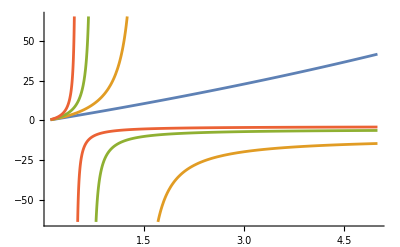

```mathematica
nur = 3.0*10^(17)
myl={nbe[nur,0.005,T], nbe[nur,0.1,T]   ,   nbe[nur,0.2,T] ,   nbe[nur,0.3,T]}
Plot[myl,{T,10*10^6,500*10^6}]
```

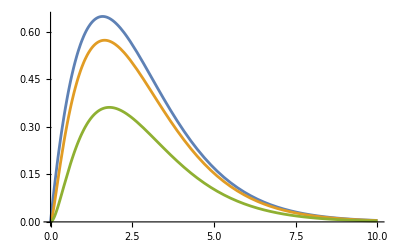

```mathematica
Plot[{x1^2*fbe[x1,0],x1^2*fbe[x1,0.1],x1^2*fbe[x1,0.5]},{x1,0,10}]
```

```mathematica
A=2;
k=1;
x0=1.0;
```

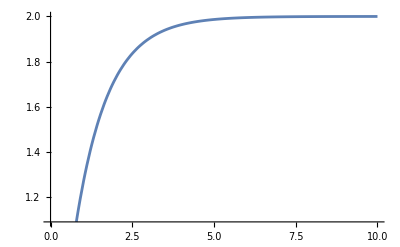

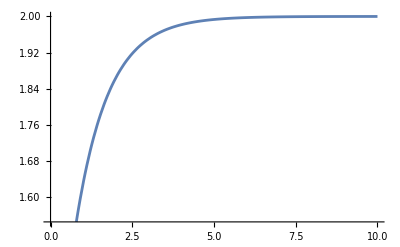

```mathematica
y1[x_]:=A*(x0-Exp[-k*x]);
Plot[y1[x1],{x1,0,10}]
```

## Rates of Change of ni, Te, Tr and Ti CHECK THE UNITS

```mathematica
(**)
f1[t_,ni_,te_,ti_, tr_]:=-(ni^2)*sigvdt[ti];      (* dni/dt *)
f2[t_,ni_,te_,ti_, tr_]:=(2/(3*ne))*((eal*(1-fali[te]))*ni*sigvdt[ti]   +pei[ne,ni,Ni-2*ni,te,ti] - prad[ni,te,ti,tr] );(* dte/dt *) 
f3[t_,ni_,te_,ti_, tr_]:=(2/(3*(ni+ni0)))*((eal*fali[te]+(3*ti/2))*(sigvdt[ti]*ni^2)-pei[ne,ni,Ni-2*ni,te,ti]); (* dti/dt *) 
f4[t_,ni_,te_,ti_, tr_]:=((h*c)^3/(32*Pi*f[al, tr, te ]))*prad[ni,te,ti,tr];      (* dtr/dt *)
```

```mathematica
(**)
niini=1;te0=0.1; ti=0.1;
t0=0;
tf=10;(*final time*)
h=0.1;(*step size*)
```

```mathematica
(**)
(*Runge-Kutta method implementation for the coupled system*)
rk4Step[t_,ni_,te_,ti_, tr_,h_]:=Module[{k1,k2,k3,k4,l1,l2,l3,l4,m1,m2,m3,m4,n1,n2,n3,n4},
k1=h f1[t,ni,te,ti,tr];
l1=h f2[t,ni,te,ti,tr];
m1=h f3[t,ni,te,ti,tr];
n1=h f4[t,ni,te,ti,tr];

k2=h f1[t+h/2,ni+k1/2,te+l1/2, ti+m1/2, tr+n1/2];
l2=h f2[t+h/2,ni+k1/2,te+l1/2, ti+m1/2, tr+n1/2];
m2=h f3[t+h/2,ni+k1/2,te+l1/2, ti+m1/2, tr+n1/2];
n2=h f4[t+h/2,ni+k1/2,te+l1/2, ti+m1/2, tr+n1/2];

k3=h f1[t+h/2,ni+k2/2,te+l2/2,ti+m2/2, tr+n2/2];
l3=h f2[t+h/2,ni+k2/2,te+l2/2,ti+m2/2, tr+n2/2];
m3=h f3[t+h/2,ni+k2/2,te+l2/2,ti+m2/2, tr+n2/2];
n3=h f4[t+h/2,ni+k2/2,te+l2/2,ti+m2/2, tr+n2/2];

k4=h f1[t+h,ni+k3,te+l3, ti+m3, tr+n3];
l4=h f2[t+h,ni+k3,te+l3, ti+m3, tr+n3];
m4=h f3[t+h,ni+k3,te+l3, ti+m3, tr+n3];
n4=h f4[t+h,ni+k3,te+l3, ti+m3, tr+n3];

{ni+(k1+2 k2+2 k3+k4)/6,te+(l1+2 l2+2 l3+l4)/6  ,ti+(m1+2 m2+2 m3+m4)/6 ,tr+(n1+2 n2+2 n3+n4)/6  }];
```

```mathematica
(**)
rk4Solve[t0_,niini_,te0_, ti0_,tr0_ ,h_,tf_]:=Module[{t=t0,ni=niini,te=te0, ti=ti0, tr=tr0,sol={{t0,niini,te0, ti0}}},
While[t<tf,
{ni,te,ti,tr}=rk4Step[t,ni,te,ti, tr,h];t=t+h;
AppendTo[sol,{t,ni,te,ti, tr}];];sol];
```

```mathematica
(**)
(*Solve the coupled differential equations*)
solution=rk4Solve[t0,niini,te0,ti0, tr0,h,tf];
(*Extract solutions for x(t) and y(t)*)
nisol=solution[[All,{1,2}]];
tesol=solution[[All,{1,3}]];
tisol=solution[[All,{1,4}]];
trsol=solution[[All,{1,5}]];

(*Plot the solutions*)
ListLinePlot[{nisol,tesol,tisol},PlotMarkers->Automatic,PlotLegends->{"ni(t)","te(t)","ti(t)","tr(t)"},PlotLabels->"Expressions",PlotTheme->"Detailed",AxesLabel->{"t","Value"}]
```